```mathematica
<<PhysicalConstants`
<<Units`
<<PlotLegends`
```

```mathematica
α=FineStructureConstant;
c=SpeedOfLight;
n=1.00153;
λ0=Convert[ElectronComptonWavelength, Nano Meter]/(Nano Meter);
me=Convert[ElectronMass c c,Giga ElectronVolt]/(Giga ElectronVolt);
mpi=0.13957;
```

```mathematica
Ang[β_]=1/(n β);
Ang2[β_]=(√(1-β^2))/β λ0/λuv (n^2-1)/(2 n^2);
λuv=190;
```

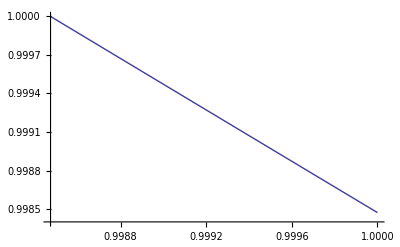

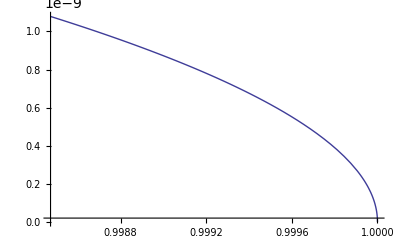

```mathematica
Plot[Ang[β],{β,1/n,1},AxesOrigin->{1/n,0.9984}]
Plot[Ang2[β],{β,1/n,1},AxesOrigin->{1/n,0.2 10^-10}]
```

```mathematica
θ=ArcCos[1/(n β)];
βmin=1/n;
```

```mathematica
f[λ1_,λ2_]=Convert[2 π α Sin[θd]^2(λ2-λ1)/(λ1 λ2)  (1/(Nano Meter)), (1/(Centi Meter))]  (Centi Meter);
```

```mathematica
Ix[λ_]=
```

```mathematica
f[400,700]
f[190,700]
```

491.257 Sin[θd]^2

1758.18 Sin[θd]^2

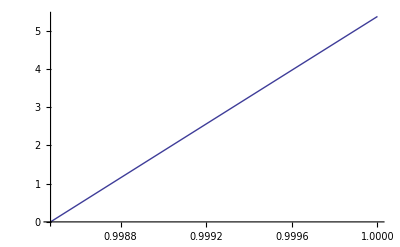

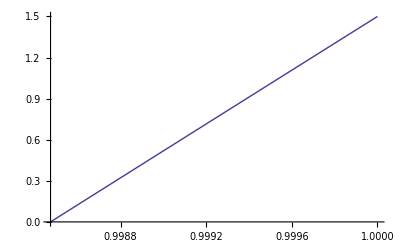

```mathematica
Plot[f[190,700],{β,1/n,1},AxesOrigin->{1/n,0}]
Plot[f[400,700],{β,1/n,1},AxesOrigin->{1/n,0}]
```

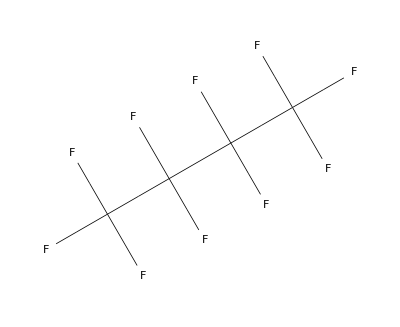

```mathematica
ChemicalData["CID9638"]
```

```mathematica
λ0=ElectronComptonWavelength;
```

```mathematica
Λ=Convert[(√(1-βmin^2))/βmin λ0,Nano Meter];
λmin = 190 Nano Meter;
λmax = 700 Nano Meter;
(Λ/λmin (n^2 -1)/(2 n^2)) 
(Λ/λmax (n^2 -1)/(2 n^2))
```

1.07874×10^-9

2.928×10^-10

```mathematica
Nx[λ1_,λ2_,β_]=Assuming[{λ1>0,λ2>0},2 π α ∫_λ1^λ2 1/λ^2 (1 - 1/(n^2 β^2)) ⅆλ] 10^9
```

ConditionalExpression[(4.58506×10^7 (0.996947 λ1-1. β^2 λ1-0.996947 λ2+1. β^2 λ2))/(β^2 λ1 λ2),λ1<λ2]

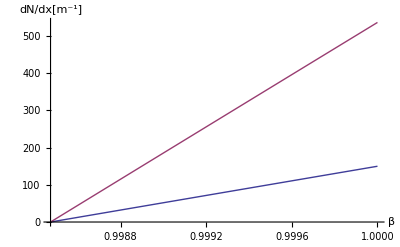

```mathematica
Plot[{Nx[400,700,β],Nx[190,700,β]},{β,1/n,1},AxesOrigin->{1/n,0},AxesLabel->{"β","dN/dx[m^-1]"}]
```

```mathematica
Series[((nn^2-1)^(1/3))/(2 nn^2),{nn,1,10}]//N
```

0.629961 (nn-1.)^(1/3)-1.15493 (nn-1.)^(4/3)+1.6624 (nn-1.)^(7/3)-2.165 (nn-1.)^(10/3)+2.66599 (nn-1.)^(13/3)-3.16638 (nn-1.)^(16/3)+3.66655 (nn-1.)^(19/3)-4.16661 (nn-1.)^(22/3)+4.66664 (nn-1.)^(25/3)-5.16666 (nn-1.)^(28/3)+O[nn-1.]^(31/3)

```mathematica
((n^2-1)^(1/3))/(2 n^2)
```

0.0723869

```mathematica
1/n
```

```mathematica
n
```

1.00153

```mathematica
γth=n/(√(n^2-1))
```

18.0983

```mathematica
√((me γth)^2 - me^2)*1000
√((mpi γth)^2 -mpi^2)
```

9.23407

2.52212

```mathematica
ChemicalData["CID9638"]
```

-Graphics-

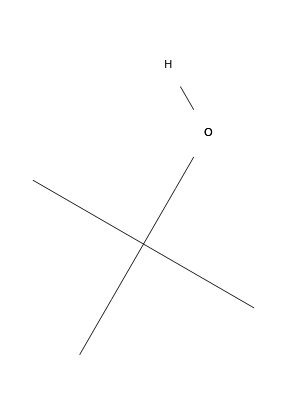

```mathematica
ChemicalData["CID6386"]
```

```mathematica
7.5
3.5
2

12
12
5.5
```

```mathematica
2 15.45+20 3.75
```

105.9

```mathematica
1/ϵ
```

```mathematica
1/2-1/ⅇ//N
```

0.132121

```mathematica
ⅇ^16//N
```

8.88611×10^6

```mathematica
Solve[Log[2,x/7]==16,x]
```

{{x→458752}}

```mathematica
tab1=Table[β,{β,βmin,1,0.00001}];
```

```mathematica
tab1[[2]]
```

0.998482

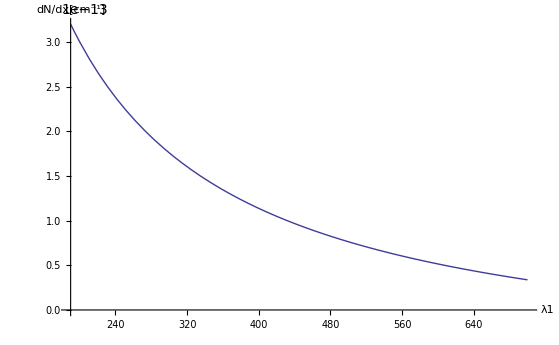

```mathematica
Plot[(657.0146924157378 (1.1368683772161603*^-13-1.1102230246251565*^-16 λ1))/λ1,{λ1,190,700},AxesOrigin->{190,0},AxesLabel->{"λ1","dN/dx[cm^-1]"}]
```

```mathematica
Length[tab1]/25//N
```

6.12

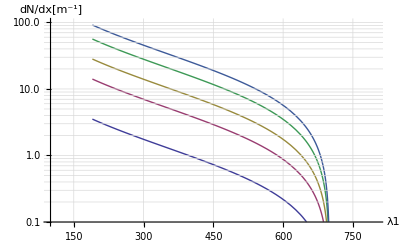

```mathematica
LogPlot[{Nx[λ1,700,tab1[[2]]],Nx[λ1,700,tab1[[5]]],Nx[λ1,700,tab1[[9]]],Nx[λ1,700,tab1[[17]]],Nx[λ1,700,tab1[[27]]]},{λ1,190,700},AxesLabel->{"λ1","dN/dx[m^-1]"},PlotRange->{{100,800},{0.1,100}}, GridLines->Automatic,PlotLegend->{"sine", "cosine"}]
```

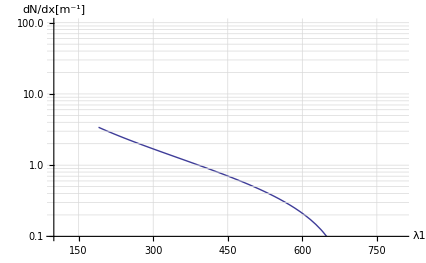

```mathematica
LogPlot[Nx[λ1,700,0.998482],{λ1,190,700},AxesLabel->{"λ1","dN/dx[m^-1]"},PlotRange->{{100,800},{0.1,100}}, GridLines->Automatic]
```

```mathematica
Convert[Ampere/Watt,ElectronVolt/Joule]
```

Convert::incomp: Incompatible units in Ampere/Watt and ElectronVolt/Joule.

Ampere/Watt